### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/15

### Keywords

Details

# Model 1.5

Model 1.5 is the model for the dynamics of malaria parasites in an infected host proposed by Anderson, May and Gupta (1989, Parasitology). It is the model with no immunological responses (equation 4.1-4.3 in the original paper; See below). The rate of change of uninfected and infected red blood cells and merozoites are considered in the model.

-Graphics-

model | the model ID
lambda | model constant (see equation 4.1)
mu | model constant (see equation 4.1)
alpha | model constant (see equation 4.2 & 4.3)
beta | model constant (see equation 4.1-4.3)
r | model constant (see equation 4.3)
d | model constant (see equation 4.3)
initx | initial number (at t = 0) of uninfected red blood cells
inity | initial number (at t =0) of infected red blood cells
inits | initial number (at t = 0) of merozoites
runsteps | number of the model run steps
stepsize | the time step size
outform | the output form (model 1.5 has only one output form (0))

List of model 1.5 parameters.

The output of model 1.5 is  the list of the number of uninfected red blood cells, infected red blood cell and merozoites over time from solving the equations 4.1-4.3.

Example of the output of model 1.5

```mathematica
lsout=IDVL["mod1_5.in"];
```

******INDIVARIA*****

model: 1.5

outform: 0

********************

model: 1.5

lambda: 1.

mu: 0.00833

beta: 0.1

alpha: 0.2

r: 16.

d: 72

initx: 10000

inity: 1.

inits: 0.

runsteps: 600

stepsize: 0.1

outform: 0

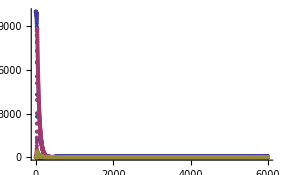

```mathematica
ListPlot[{lsout[[All,2]],lsout[[All,3]],lsout[[All,4]]}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses